```mathematica
SetDirectory[NotebookDirectory[]];
data = Drop[Flatten[Import["energie_test.TKA", "table"]], 2];
data = data[[;;300]];
```

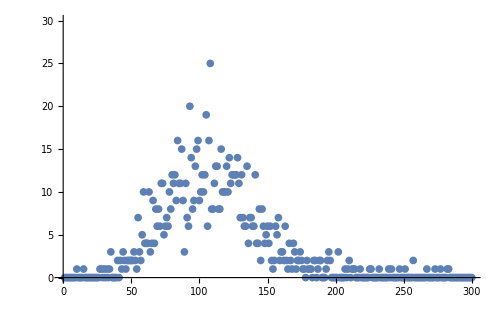

```mathematica
ListPlot[data, PlotRange->{{0, 300},{0, 30}}, ImageSize->500]
```

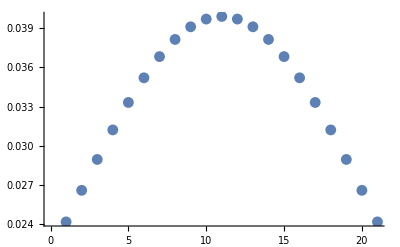

```mathematica
gaus = Table[PDF[NormalDistribution[0, 10], x], {x, -10, 10, 1}];
ListPlot[gaus]
```

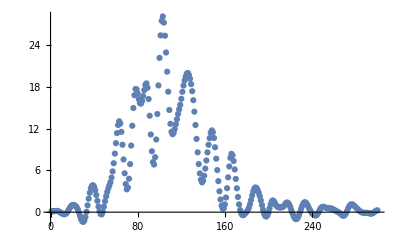

```mathematica
dec = ListDeconvolve[gaus, data];
ListPlot[dec]
```